Логаш Полина Вариант 7

1. Задаем начальные данные

```mathematica
Subscript[x, 0]=0; Subscript[x, 1]=π/4; Subscript[x, 2]=π/2; n=2;
f[x_]=Sin[x]^3;
m=1;
NN=(m+1)*(n+1)-1;
```

2. Строим интерполяционный многочлен Эрмита

```mathematica
P[x_]=∑_(k=0)^NN Subscript[a, k]*x^k;
eqv=Table[(D[P[x],{x,j}]//.x->Subscript[x, k])==(D[f[x],{x,j}]//.x->Subscript[x, k]),{j,0,m},{k,0,n}]//Flatten;
koef=Solve[eqv,{}]//Flatten;
P[x_]=P[x]//.koef//N
```

-0.272268 x^2+2.06433 x^3-1.47607 x^4+0.277869 x^5

3. Проверяем выполнение интерполяционных условий

```mathematica
Table[((D[P[x],{x,j}]//.x->Subscript[x, k])-(D[f[x],{x,j}]//.x->Subscript[x, k])//Chop)==0,{j,0,m},{k,0,n}]
```

{{True,True,True},{True,True,True}}

4. Строим интерполяционный мноочлен Эрмита с помощью с помощью встроенной функции InterpolatingPolinominal и проверяем совпадение построенного и контрольного полиномов;

```mathematica
Tbl=Table[{Subscript[x, i],Table[(D[f[x],{x,j}]//.x->Subscript[x, i]),{j,0,m}]},{i,0,n}];
P1[x_]=InterpolatingPolynomial[Tbl,x]//Expand;
N[P[x]-P1[x]]//Chop
```

0

5. Изображаем исходную систему точек и полученный интерполяционный многочлен в одной системе координат;

{{0,0},{π/4,1/(2 √2)},{π/2,1}}

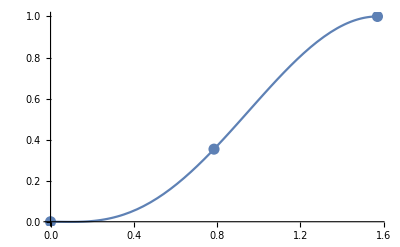

```mathematica
Tb=Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]
Gr1=ListPlot[Tb,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2,PlotRange->Automatic]
```

6. Оцениваем погрешность интерполирования на отрезке;

```mathematica
M1=Maximize[{D[f[x],{x,NN+1}],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]];
M2=Minimize[{D[f[x],{x,NN+1}],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]];
M=Max[{Abs[M1],Abs[M2]}];
```

```mathematica
ω[t_]=∏_(i=0)^n (t-Subscript[x, i])^(m+1);
Subscript[M, ω]=Maximize[{Abs[ω[x]],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]]//N;
R=M/((NN+1)!)*Subscript[M, ω]//N
```

0.008838

7. Изображаем графики абсолютной погрешности и ее оценки в одной системе координат;

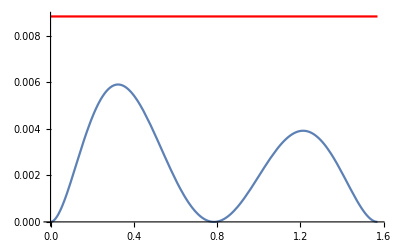

```mathematica
Gr3=Plot[Abs[f[x]-P[x]],{x,Subscript[x, 0],Subscript[x, n]}];
Gr4=Plot[R,{x,Subscript[x, 0],Subscript[x, n]},PlotStyle->Red];
Show[Gr3,Gr4,PlotRange->All]
```

8. Убеждаемся что значения абсолютной погрешности интерполирования не превосходяя ее оцкенки;

```mathematica
MR1=Maximize[{f[x]-P[x],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]];
MR2=Minimize[{f[x]-P[x],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]];
MR=Max[{Abs[MR1],Abs[MR2]}];
MR≤R
```

True

9. Проверяем свойство инвариантности;

```mathematica
Unprotect[Power];
0^0:=1
Table[{f[x_]=x^j,f[x]==∑_(k=0)^NN Subscript[a, k]*x^k//.(Solve[Table[(D[∑_(k=0)^NN Subscript[a, k]*x^k,{x,j}]//.x->Subscript[x, k])==(D[f[x],{x,j}]//.x->Subscript[x, k]),{j,0,m},{k,0,n}]//Flatten,{}]//Flatten)},{j,0,NN+1}]
```

{{1,True},{x,True},{x^2,True},{x^3,True},{x^4,True},{x^5,True},{x^6,x^6==-1/64 π^4 x^2+(3 π^3 x^3)/16-(13 π^2 x^4)/16+(3 π x^5)/2}}